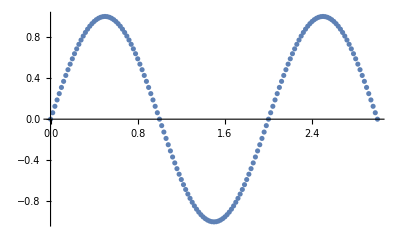
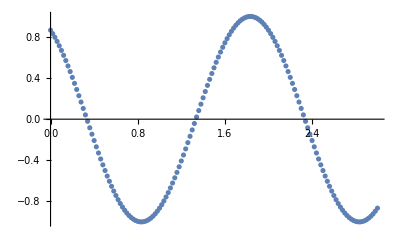
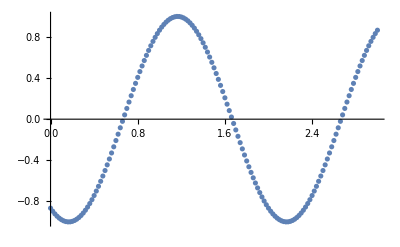

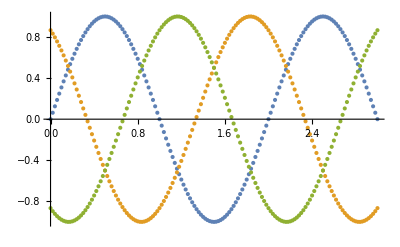

-Graphics-

-Graphics-

```mathematica
glgl=GridLines->{{
{1/6,Green},{2/6,Green},{3/6,Green},{4/6,Green},{5/6,Green},
{7/6,Green},{8/6,Green},{9/6,Green},{10/6,Green},{11/6,Green},
{1,Red},{2,Red},{3,Red}},None};
SSA[offset_,length_,high_]:=Table[
{x,high*Sin[x*π+offset*π]},
{x,0,length,0.02}];
A1=SSA[0,3,1];A2=SSA[2/3,3,1];A3=SSA[-2/3,3,1];
B12=A1-A2;
B23=A2-A3;
B31=A3-A1;
FFF[s1_,s2_,s3_]:=ListPlot[{s1,s2,s3},glgl]
{ListPlot[A1],ListPlot[A2],ListPlot[A3]}
ListPlot[{A1,A2,A3},glgl]
FFF[A1,A2,A3]
FFF[B1,B2,B3]
```